```mathematica
Clear[Lx, Ly, A, l1, l2, mL,
 SX2DDis, SX2DPDis,
 SY2DDis, SY2DPDis,
 CX2DDis, CX2DPDis,
 CY2DDis, CY2DPDis,
 Cons]
```

```mathematica
Lx = 28;
Ly =28;
l1 = 7;
l2 = 14;
mL = 14;
A = Lx*Ly + l2
NOrbitals = 2*A;
```

798

```mathematica
(*-----------------------------------------------*)
```

```mathematica
SX2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SX2DDis[[a + b Lx, a + 1 + b Lx]]=I/2, SX2DDis[[a + 1 + b Lx, a + b Lx]] = -I/2},{a,1, Lx -1}],{b,0, l1-1}]
Do[Do[{SX2DDis[[a + b(Lx+1)+ l1 Lx, a + 1 + b(Lx+1)+l1 Lx]]=I/2, SX2DDis[[a + 1 + b(Lx +1)+l1 Lx, a + b(Lx + 1) + l1 Lx]]= - I/2},{a,1,Lx}],{b,0,l2 -1}]
Do[Do[{SX2DDis[[a + b Lx + Lx(l1 + l2) + l2, a + b Lx + Lx(l1 + l2) + l2 + 1]]=I/2, SX2DDis[[a + b Lx + Lx(l1 + l2) + l2 + 1, a + b Lx + Lx(l1 + l2) + l2 ]]=-I/2},{a,1,Lx-1}],{b,0,Ly - (l1 + l2) -1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CX2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CX2DDis[[a + b Lx, a + 1 + b Lx]]=1/2, CX2DDis[[a + 1 + b Lx, a + b Lx]] = 1/2},{a,1, Lx -1}],{b,0, l1-1}]
Do[Do[{CX2DDis[[a + b(Lx+1)+ l1 Lx, a + 1 + b(Lx+1)+l1 Lx]]=1/2, CX2DDis[[a + 1 + b(Lx +1)+l1 Lx, a + b(Lx + 1) + l1 Lx]]= 1/2},{a,1,Lx}],{b,0,l2 -1}]
Do[Do[{CX2DDis[[a + b Lx + Lx(l1 + l2) + l2, a + b Lx + Lx(l1 + l2) + l2 + 1]]=1/2, CX2DDis[[a + b Lx + Lx(l1 + l2) + l2 + 1, a + b Lx + Lx(l1 + l2) + l2 ]]=1/2},{a,1,Lx-1}],{b,0,Ly - (l1 + l2) -1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
(**--Periodic in x--**)
```

```mathematica
SX2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{SX2DPDis[[(b+1)Lx,b Lx + 1]]=I/2,SX2DPDis[[b Lx + 1,(b+1) Lx ]]=-I/2},{b,0, l1-1}]
Do[{SX2DPDis[[(b+1)(Lx + 1)+l1 Lx, b(Lx + 1)+l1 Lx+1]]=I/2,SX2DPDis[[b(Lx + 1)+l1 Lx+1,(b+1)(Lx + 1)+l1 Lx]]=-I/2},{b,0, l2-1}]
Do[{SX2DPDis[[(b+1) Lx + Lx(l1 + l2) + l2, b Lx + 1 + Lx(l1 + l2) + l2]]=I/2, SX2DPDis[[b Lx + 1 + Lx(l1 + l2) + l2, (b+1) Lx + Lx(l1 + l2) + l2]]=-I/2},{b,0,Ly-(l1+l2)-1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CX2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{CX2DPDis[[(b+1)Lx,b Lx + 1]]=1/2,CX2DPDis[[b Lx + 1,(b+1) Lx ]]=1/2},{b,0, l1-1}]
Do[{CX2DPDis[[(b+1)(Lx + 1)+l1 Lx, b(Lx + 1)+l1 Lx+1]]=1/2,CX2DPDis[[b(Lx + 1)+l1 Lx+1,(b+1)(Lx + 1)+l1 Lx]]=1/2},{b,0, l2-1}]
Do[{CX2DPDis[[(b+1) Lx + Lx(l1 + l2) + l2, b Lx + 1 + Lx(l1 + l2) + l2]]=1/2, CX2DPDis[[b Lx + 1 + Lx(l1 + l2) + l2, (b+1) Lx + Lx(l1 + l2) + l2]]=1/2},{b,0,Ly-(l1+l2)-1}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
SY2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{SY2DDis[[a + b Lx, a + (b+1)Lx]]=I/2,SY2DDis[[a + (b+1) Lx, a + b Lx]]=-I/2},{a,1,Lx}],{b,0,l1-2}]
Do[Do[{SY2DDis[[a + b(Lx + 1) + l1 Lx, a + (b+1)(Lx + 1)+l1 Lx]]=I/2,SY2DDis[[a + (b+1)(Lx + 1) + l1 Lx, a + b(Lx + 1)+l1 Lx]]=-I/2},{a,1, Lx + 1}],{b,0,l2 -2}]
Do[Do[{SY2DDis[[a + b Lx + Lx (l1 + l2) + l2, a + (b+1)Lx + Lx (l1 + l2) + l2]]= I/2, SY2DDis[[a + (b+1)Lx + Lx (l1 + l2) + l2, a + b Lx + Lx (l1 + l2) + l2]] = -I/2},{a ,1,Lx}],{b,0, Ly - (l1 + l2) - 2}]
Do[{SY2DDis[[a + (l1-1) Lx, a + l1 Lx]]=I/2, SY2DDis[[a + l1 Lx, a + (l1-1)Lx]]=-I/2},{a,1,mL}]
Do[{SY2DDis[[a + mL + (l1-1)Lx, a + mL + 1+ l1 Lx]]=I/2, SY2DDis[[a + mL + 1+ l1 Lx, a + mL + (l1-1)Lx]]=-I/2},{a,1,Lx-mL}]
Do[{SY2DDis[[a+(l1 + l2)Lx+l2-(Lx+1), a + (l1 + l2)Lx + l2]]=I/2, SY2DDis[[a + (l1 + l2)Lx + l2, a + (l1+l2)Lx + l2-(Lx +1)]]=-I/2},{a,1,mL}]
Do[{SY2DDis[[a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx+1), a + mL + (l1 + l2)Lx + l2]]=I/2, SY2DDis[[a + mL + (l1 + l2)Lx + l2, a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx + 1)]]=-I/2},{a,1,Lx-mL}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CY2DDis=Table[0,{a,1,A},{b,1,A}];
Do[Do[{CY2DDis[[a + b Lx, a + (b+1)Lx]]=1/2,CY2DDis[[a + (b+1) Lx, a + b Lx]]=1/2},{a,1,Lx}],{b,0,l1-2}]
Do[Do[{CY2DDis[[a + b(Lx + 1) + l1 Lx, a + (b+1)(Lx + 1)+l1 Lx]]=1/2,CY2DDis[[a + (b+1)(Lx + 1) + l1 Lx, a + b(Lx + 1)+l1 Lx]]=1/2},{a,1, Lx + 1}],{b,0,l2 -2}]
Do[Do[{CY2DDis[[a + b Lx + Lx (l1 + l2) + l2, a + (b+1)Lx + Lx (l1 + l2) + l2]]= 1/2, CY2DDis[[a + (b+1)Lx + Lx (l1 + l2) + l2, a + b Lx + Lx (l1 + l2) + l2]] = 1/2},{a ,1,Lx}],{b,0, Ly - (l1 + l2) - 2}]
Do[{CY2DDis[[a + (l1-1) Lx, a + l1 Lx]]=1/2, CY2DDis[[a + l1 Lx, a + (l1-1)Lx]]=1/2},{a,1,mL}]
Do[{CY2DDis[[a + mL + (l1-1)Lx, a + mL + 1+ l1 Lx]]=1/2, CY2DDis[[a + mL + 1+ l1 Lx, a + mL + (l1-1)Lx]]=1/2},{a,1,Lx-mL}]
Do[{CY2DDis[[a+(l1 + l2)Lx+l2-(Lx+1), a + (l1 + l2)Lx + l2]]=1/2, CY2DDis[[a + (l1 + l2)Lx + l2, a + (l1+l2)Lx + l2-(Lx +1)]]=1/2},{a,1,mL}]
Do[{CY2DDis[[a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx+1), a + mL + (l1 + l2)Lx + l2]]=1/2, CY2DDis[[a + mL + (l1 + l2)Lx + l2, a + (mL + 1) + (l1 + l2) Lx + l2 - (Lx + 1)]]=1/2},{a,1,Lx-mL}]
```

```mathematica
(**---------------Periodic in y-----------------**)
```

```mathematica
SY2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{SY2DPDis[[Lx (Ly-1)+l2+a,a]]=I/2, SY2DPDis[[a, Lx(Ly-1)+l2+a]]=-I/2},{a,1,Lx}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
CY2DPDis=Table[0,{a,1,A},{b,1,A}];
Do[{CY2DPDis[[Lx (Ly-1)+l2+a,a]]=1/2, CY2DPDis[[a, Lx(Ly-1)+l2+a]]=1/2},{a,1,Lx}]
```

```mathematica
(*-----------------------------------------------*)
```

```mathematica
Cons=Table[0,{a,1,A},{b,1,A}];
Do[Cons[[a,a]]=1,{a,1,A}]
```

```mathematica
(*----------------------------------------------------------------------------------------------------------*)
(*----------------------------------------------------------------------------------------------------------*)
```

```mathematica
(**--- Check with matrices from octave ---**)
```

```mathematica
(***----Clear[sxnpReal, sxnpImag, synpReal, synpImag, cxnpReal, cxnpImag, cynpReal,cynpImag,
sxpReal, sxpImag, sypReal, sypImag, cxpReal, cxpImag, cypReal,cypImag] ----***)
```

```mathematica
(*--- sxnpReal = Import["sxnpReal.dat"];
sxnpImag = Import["sxnpImag.dat"];
synpReal = Import["synpReal.dat"];
synpImag = Import["synpImag.dat"];
cxnpReal = Import["cxnpReal.dat"];
cxnpImag = Import["cxnpImag.dat"];
cynpReal = Import["cynpReal.dat"];
cynpImag = Import["cynpImag.dat"];

sxpReal = Import["sxpReal.dat"];
sxpImag = Import["sxpImag.dat"];
sypReal = Import["sypReal.dat"];
sypImag = Import["sypImag.dat"];
cxpReal = Import["cxpReal.dat"];
cxpImag = Import["cxpImag.dat"];
cypReal = Import["cypReal.dat"];
cypImag = Import["cypImag.dat"]; ---*)
```

```mathematica
(*--- {Max[sxnpReal - Re[SX2DDis]],
Max[sxnpImag - Im[SX2DDis]],
Max[synpReal - Re[SY2DDis]],
Max[synpImag - Im[SY2DDis]],
Max[cxnpReal - Re[CX2DDis]],
Max[cxnpImag - Im[CX2DDis]],
Max[cynpReal - Re[CY2DDis]],
Max[cynpImag - Im[CY2DDis]],
Max[sxpReal - Re[SX2DDis]-Re[SX2DPDis]],
Max[sxpImag - Im[SX2DDis]- Im[SX2DPDis]],
Max[sypReal - Re[SY2DDis]-Re[SY2DPDis]],
Max[sypImag - Im[SY2DDis]-Im[SY2DPDis]],
Max[cxpReal - Re[CX2DDis]-Re[CX2DPDis]],
Max[cxpImag - Im[CX2DDis]-Im[CX2DPDis]],
Max[cypReal - Re[CY2DDis]-Re[CY2DPDis]],
Max[cypImag - Im[CY2DDis]-Im[CY2DPDis]],
Min[sxnpReal - Re[SX2DDis]],
Min[sxnpImag - Im[SX2DDis]],
Min[synpReal - Re[SY2DDis]],
Min[synpImag - Im[SY2DDis]],
Min[cxnpReal - Re[CX2DDis]],
Min[cxnpImag - Im[CX2DDis]],
Min[cynpReal - Re[CY2DDis]],
Min[cynpImag - Im[CY2DDis]],
Min[sxpReal - Re[SX2DDis]-Re[SX2DPDis]],
Min[sxpImag - Im[SX2DDis]- Im[SX2DPDis]],
Min[sypReal - Re[SY2DDis]-Re[SY2DPDis]],
Min[sypImag - Im[SY2DDis]-Im[SY2DPDis]],
Min[cxpReal - Re[CX2DDis]-Re[CX2DPDis]],
Min[cxpImag - Im[CX2DDis]-Im[CX2DPDis]],
Min[cypReal - Re[CY2DDis]-Re[CY2DPDis]],
Min[cypImag - Im[CY2DDis]-Im[CY2DPDis]]} ---*)
```

```mathematica
Clear[σ0,σ1,σ2,σ3,HamiltonianQAHIDisloc]
```

```mathematica
σ0=PauliMatrix[0];
σ1=PauliMatrix[1];
σ2=PauliMatrix[2];
σ3=PauliMatrix[3];
```

```mathematica
HamiltonianQAHIDisloc[t_,t0_,m_,α_]:=t*(KroneckerProduct[SX2DDis+α*SX2DPDis,σ1]+KroneckerProduct[SY2DDis+α*SY2DPDis, σ2])+KroneckerProduct[-m*Cons+t0*(CX2DDis+CY2DDis+α*CX2DPDis+α*CY2DPDis),σ3]
```

```mathematica
(*--------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[val,vec,ValVecAHI,ValAHI,ValAHIRange]
```

```mathematica
{val,vec}=Eigensystem[HamiltonianQAHIDisloc[1.0,1.0,1.0,1.0]];
```

```mathematica
ValVecAHI=SortBy[Transpose[{val,vec}],First];
```

```mathematica
ValAHI=Table[{j,Re[ValVecAHI[[j,1]]]},{j,1,2A}];
```

```mathematica
ValAHIRange=Table[ValAHI[[j,2]],{j,1,2 A}];
```

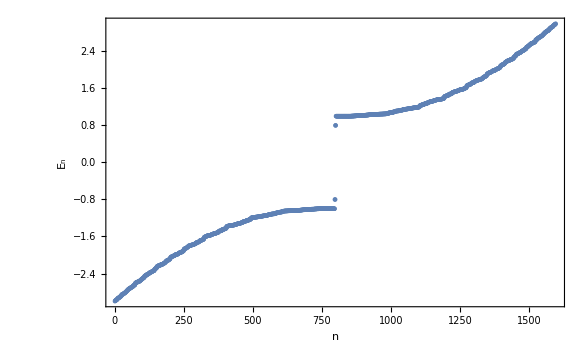

```mathematica
Show[ListPlot[ValAHI,Frame-> True,Axes-> False,PlotRange-> {{0,2A},{Min[ValAHIRange],Max[ValAHIRange]}}],(*Plot[0,{x,0,2A},PlotStyle-> Red],*)BaseStyle-> 14,FrameStyle-> Black,FrameLabel-> {"n","E_n"}]
```

```mathematica
(**---------------------------------------------------------**)
```

```mathematica
Clear[Xaxis, Yaxis1, Yaxis2, Yaxis3, P3, P4, P2B]
```

```mathematica
Xaxis=Table[{{1,j},{Lx+1,j}},{j,1,Ly,1}];
```

```mathematica
Dimensions[Xaxis]
```

{28,2,2}

```mathematica
P3=Graphics[ListPlot[Table[Xaxis[[j]],{j,1,Ly}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,8,21,28},None},{{1,28/2,29},None}},BaseStyle-> 18];
```

```mathematica
Yaxis1=Table[{{j,1},{j,Ly}},{j,1,mL,1}];
```

```mathematica
Yaxis2={{mL+1,l1+1},{mL+1,l1+l2}};
```

```mathematica
Yaxis3=Table[{{j,1},{j,Ly}},{j,mL+2,Lx+1,1}];
```

```mathematica
Dimensions[Yaxis3]
```

{14,2,2}

```mathematica
P4=Show[ListPlot[Table[Yaxis1[[j]],{j,1,mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}},PlotRange->{{1,Lx+1},{1,Ly}},Frame-> True,Axes-> False,AspectRatio->1],
ListPlot[Yaxis2,Joined-> True,PlotStyle-> Lighter[Gray]],
ListPlot[Table[Yaxis3[[j]],{j,1,Lx-mL}],Joined-> True,PlotStyle-> {{Lighter[Gray]}}]
];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
P2B=Show[Graphics[{},

Frame->True,
FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},
FrameTicks-> {{{1,Round[Ly/4]+1,Round[3 Ly/4],Ly},None},{{1,Round[Lx/2]+1,Lx+1},None}},BaseStyle-> 18,
PlotRange-> {{1,Lx+1},{1,Ly}}
]];
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------------------------------*)
```

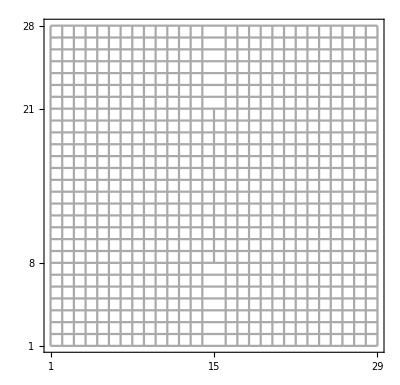

```mathematica
P5=Show[P2B,P3,P4]
```

```mathematica
LineUp[x_]:=((1+√5)/2)^-1*(x-1)+0
LineDn[x_]:=((1+√5)/2)^-1*(x-2)-1
```

```mathematica
N[LineUp[6]]
```

3.09017

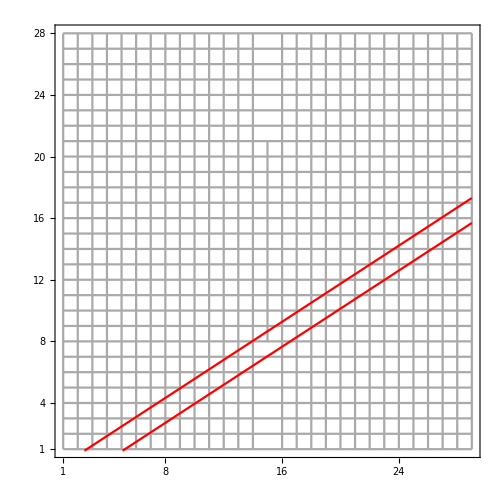

```mathematica
Show[P5,
(*Plot[2/3*(x-1)+4,{x,0,Lx},PlotStyle-> Blue],Plot[2/3*(x-2)+3,{x,0,Lx},PlotStyle-> Blue],*)
Plot[LineUp[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+1+0.1}}],
Plot[LineDn[x],{x,1,Lx+1},PlotStyle-> Red,PlotRange-> {{0.9,Lx+1+0.1},{0.9,Ly+1+0.1}}],
FrameStyle-> {{Thick,Black},{Thick,Black},{Thick,Black},{Thick,Black}},BaseStyle-> 16,
FrameTicks-> {{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None},{{{1,"1"},{4,"4"},{8,"8"},{12,"12"},{16,"16"},{20,"20"},{24,"24"},{28,"28"}},None}},
ImageSize-> 300,AspectRatio-> 1
]
```

```mathematica
(**---This function generates site number for a given coordinates and set of parameter---**)
```

```mathematica
(**---Generates 0 for non existing points, e.g. the two lines below and above dislocation centers---**)
```

```mathematica
GenerateSiteNumber[x_,y_,Lx_,Ly_,l1_,l2_,mL_]:=Piecewise[{{x+(y-1)Lx, 1≤ x ≤ mL &&1≤ y≤ l1 },{x+(y-1)Lx-1, Lx+1≥ x > mL+1 &&1≤ y≤ l1 },{x+(y-1)(Lx+1)-l1,l1<y≤(l1+l2)&&Lx+1≥ x ≥ 1 },{x+(y-1)Lx+l2,1≤ x ≤ mL &&Ly≥ y>(l1+l2)},{x+(y-1)Lx+l2-1,Lx+1≥x > mL+1 &&Ly≥y>(l1+l2)}},0]
```

```mathematica
GenerateSiteNumber[1,17,Lx,Ly,l1,l2,mL]
```

458

```mathematica
Clear[FibonListNew]
FibonListNew={};
```

```mathematica
(**---Points on the lines are not taken---**)
```

```mathematica
(**---That is why we calculate Floor[]+1 instead of Ceiling, and Ceiling[]-1 instead of Floor---**)
```

```mathematica
(**--x runs from 1 to Lx + 1--**)
```

```mathematica
Do[Do[FibonListNew=Append[FibonListNew,GenerateSiteNumber[x,y,Lx,Ly,l1,l2,mL]],{y,Max[1,Floor[LineDn[x]]+1],Min[Ly,Ceiling[LineUp[x]]-1]}],{x,1,Lx+1}]
```

```mathematica
FibonList=Sort[FibonListNew]
```

{3,4,5,33,34,62,63,64,92,93,94,122,123,151,152,153,181,182,210,211,212,241,242,243,272,273,302,303,304,333,334,335,364,365,394,395,396,425,426,455,456,457,486}

```mathematica
(**--Delete the zeros, which are generated for the non-existing lines of atoms--**)
```

```mathematica
FibonList=DeleteCases[FibonList,0]
```

{3,4,5,33,34,62,63,64,92,93,94,122,123,151,152,153,181,182,210,211,212,241,242,243,272,273,302,303,304,333,334,335,364,365,394,395,396,425,426,455,456,457,486}

```mathematica
Dimensions[FibonList]
```

{43}

```mathematica
Clear[FibonListOld, Fibonup, Fibondown, TotalFibon]
```

```mathematica
(**-- The dislocation center is 211, it is at the 19th position, and the corresponding orbital indices are 39 and 40 --**)
```

```mathematica
(**--Note-this was wrong, I missed site 62--**)
```

```mathematica
FibonListOld={3,4,5,33,34,63,64,92,93,94,122,123,151,152,153,181,182,210,211,212,241,242,243,272,273,302,303,304,333,334,335,364,365,394,395,396,425,426,455,456,457,486};
```

```mathematica
Dimensions[FibonListOld]
```

{42}

```mathematica
Fibonup = 2 * FibonList -1;
```

```mathematica
Fibondown = 2* FibonList;
```

```mathematica
TotalFibon=Flatten[{Fibonup,Fibondown}];
```

```mathematica
TotalFibon=Sort[TotalFibon];
```

```mathematica
NOrbitalsQuasi=Dimensions[TotalFibon][[1]]
```

86

```mathematica
NOrbitalsQuasi/2
```

43

```mathematica
NOrbitalsOutside = NOrbitals-NOrbitalsQuasi
```

1510

```mathematica
(*-----------------------------------------------------------------------------*)
```

```mathematica
Clear[F1,a]
```

```mathematica
F1=Table[i,{i,1,2*A}];
```

```mathematica
Dimensions[F1]
```

{1596}

```mathematica
a= Complement[F1, TotalFibon];
```

```mathematica
Dimensions[a]
```

{1510}

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HTrial,Hfbfb,HFBFB,H2d2d,H2D2D,H2dfb,H2DFB,Hfb2d,HFB2D]
```

```mathematica
HTrial=HamiltonianQAHIDisloc[1.,1.,1.0,1.0];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
Hfbfb[i_Integer,j_Integer]=0;
Do[
Do[
Hfbfb[i,j]=HTrial[[TotalFibon[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsQuasi}
]
HFBFB=Table[Hfbfb[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*---------------------------------------------------------*)
```

```mathematica
H2d2d[i_Integer,j_Integer]=0;
Do[
Do[
H2d2d[i,j]=HTrial[[a[[i]],a[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsOutside}
]
H2D2D=Table[H2d2d[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsOutside}];
```

```mathematica
(*------------------------------------------------------*)
```

```mathematica
H2dfb[i_Integer,j_Integer]=0;

Do[
Do[
H2dfb[i,j]=HTrial[[a[[i]],TotalFibon[[j]]]],
{i,1,NOrbitalsOutside}
],
{j,1,NOrbitalsQuasi}
]
H2DFB=Table[H2dfb[i,j],{i,1,NOrbitalsOutside},{j,1,NOrbitalsQuasi}];
```

```mathematica
(*-------------------------------------------------*)
```

```mathematica
Hfb2d[i_Integer,j_Integer]=0;

Do[
Do[
Hfb2d[i,j]=HTrial[[TotalFibon[[i]],a[[j]]]],
{i,1,NOrbitalsQuasi}
],
{j,1,NOrbitalsOutside}
]
HFB2D=Table[Hfb2d[i,j],{i,1,NOrbitalsQuasi},{j,1,NOrbitalsOutside}];
```

```mathematica
(*---------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[HFibonRenor,ValueFibon,VecFibon,ValVecFibon,ValFibon]
```

```mathematica
HFibonRenor=HFBFB-(HFB2D.Inverse[H2D2D].H2DFB);
```

```mathematica
{ValueFibon,VecFibon}=Eigensystem[HFibonRenor];
```

```mathematica
ValVecFibon=SortBy[Transpose[{ValueFibon,VecFibon}],First];
```

```mathematica
ValFibon=Table[{j,ValVecFibon[[j,1]]},{j,1,NOrbitalsQuasi}]//Chop;
```

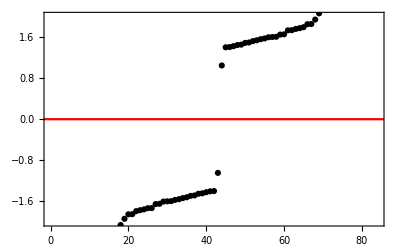

```mathematica
Show[ListPlot[ValFibon,Frame-> True,Axes-> False,BaseStyle-> 16,PlotStyle-> Black,FrameStyle-> Black,PlotRange->{{0,84},{-2,2}}],Plot[0,{x,-100,100},PlotStyle-> Red]]
```

```mathematica
(*----------- with dislocation +1 PBC ---------*)
```

```mathematica
(*----------- with dislocation -1 PBC -------*)
```

```mathematica
(*-------------- with dislocation for -1 OBC -----------------*)
```

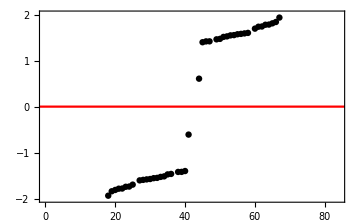
```mathematica
-Graphics-;
```

```mathematica
(*------------ with dislocation  +1 OBC -----------*)
```

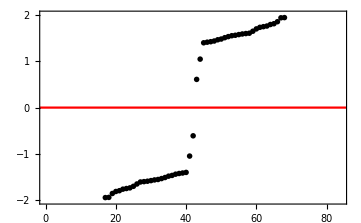
```mathematica
-Graphics-;
```

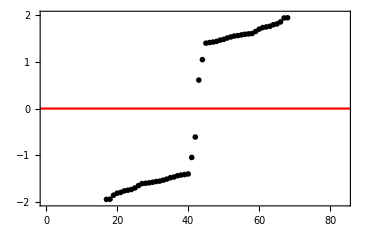
```mathematica
(*** for +1 **)
-Graphics-;
```

```mathematica
(** The 43nd and the 44th orbital have high density near the dislocation centers (39th and 40th sites) **)
```

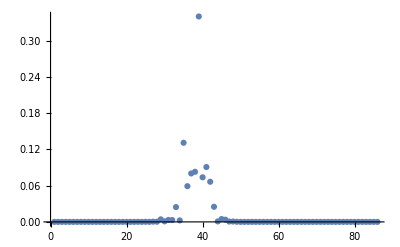

{{39}}

```mathematica
vecIndex=43;
ListPlot[Abs[ValVecFibon[[vecIndex]][[2]]]* Abs[ValVecFibon[[vecIndex]][[2]]]/Sum[Abs[ValVecFibon[[vecIndex]][[2]][[i]]]* Abs[ValVecFibon[[vecIndex]][[2]][[i]]],{i,1,84}],PlotRange->All]
Position[Abs[ValVecFibon[[vecIndex]][[2]]],Max[Abs[ValVecFibon[[vecIndex]][[2]]]]]
```

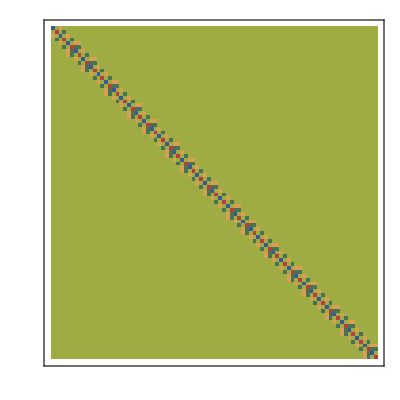

```mathematica
ArrayPlot[Re[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

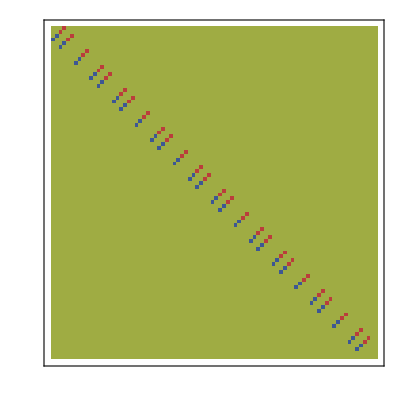

```mathematica
ArrayPlot[Im[HFBFB[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------------------------------------------*)
```

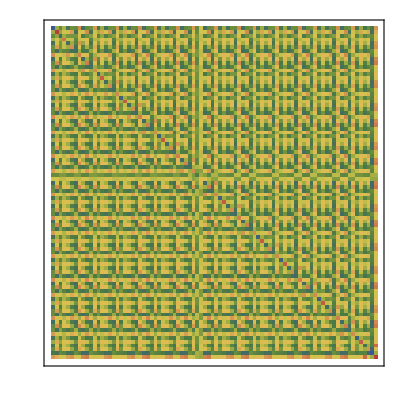

```mathematica
ArrayPlot[Re[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```

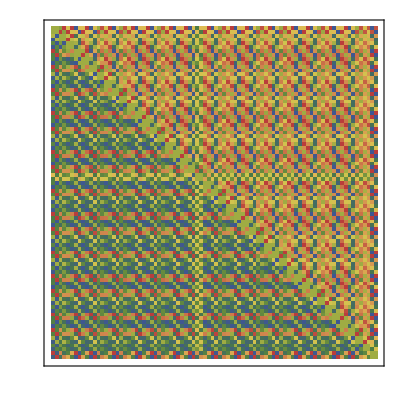

```mathematica
ArrayPlot[Im[HFibonRenor[[1;;NOrbitalsQuasi,1;;NOrbitalsQuasi]]],Frame-> True,Axes-> False,FrameStyle-> {{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}},ColorFunction->"DarkRainbow"]
```